## Sensor test 1

Just some silly folks, bouncing balls on a conference table. See the README for more.

The noise

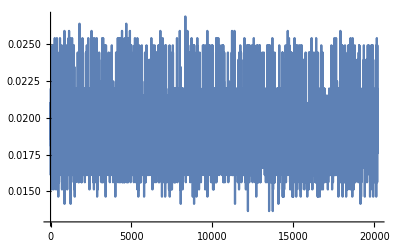

```mathematica
ListLinePlot[noise=Import["~/GitHub/piezo/Data/Test 1/01noise.dat","List"]/32767.0,PlotRange->All]
```

```mathematica
Mean[noise]//N
```

0.01942

```mathematica
StandardDeviation[noise]//N
```

0.00118009

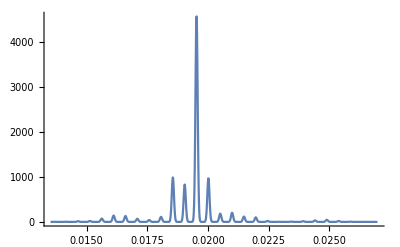

```mathematica
SmoothHistogram[noise,PlotRange->All]
```

The histogram shows the quantization!

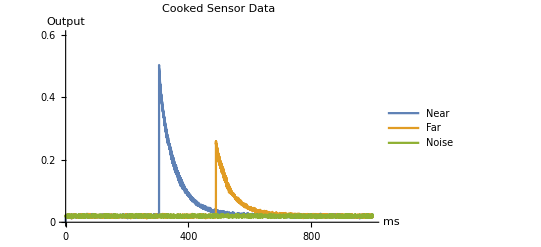

```mathematica
ListLinePlot[
{Import["~/GitHub/piezo/Data/Test 1/02near.dat","List"]/32767.0,
Import["~/GitHub/piezo/Data/Test 1/03far.dat","List"]/32767.0,Import["~/GitHub/piezo/Data/Test 1/01noise.dat","List"]/32767.0},PlotRange->{0,.6},PlotLegends->{"Near","Far","Noise"},DataRange->{0,1000},AxesLabel->{"ms","Output"},PlotStyle->Thick,PlotLabel->"Cooked Sensor Data"]
```

```mathematica
Export["~/Desktop/results1.png",%]
```

~/Desktop/results1.png